# Results concerning 1D Site Response

Joaquin Garcia-Suarez, 2019 (All rights reserved)

This notebook provides the steps to evaluate the variables that make up the results displayed in Chapter III.

## Comparison of exact solution and asymptotics (geometrical optics) corresponding to the generalized parabola distribution

The exact solution provided by Rovithis et al.(2011)

It follows the solution derived by Rovithis and collaborators in the paper titled “1D Harmonic Response of Layered Inhomogeneous Soils: Analytical Investigation”.

## Auxiliary Parameters

These are the parameters that follow the presentation of eq.(3.17):

```mathematica
λ[α_,n_,r_,δ_]:=(r/Sqrt[(1+ⅈ*δ)])/((1-n)*(1-α^(1/(2*n))));
```

```mathematica
ψ[n_]:=(1-2*n)/2;
```

```mathematica
ν[n_]:=(2*n-1)/(2(1-n));
```

## Exact Base-to-top Transfer Function

This corresponds to eq.(3.17) itself as in the text:

```mathematica
TFR[α_,n_,r_,δ_]:=2/π*((α^(1/(2*n)))^(ψ[n]-1+n))/λ[α,n,r,δ]*(BesselJ[ν[n]+1,λ[α,n,r,δ]*(α^(1/(2*n)))^(1-n)]*BesselY[ν[n],λ[α,n,r,δ]]-BesselY[ν[n]+1,λ[α,n,r,δ]*(α^(1/(2*n)))^(1-n)]*BesselJ[ν[n],λ[α,n,r,δ]])^-1
```

Asymptotics of Exact Solution (Geometrical Optics)

This transfer function mirrors eq.(3.19):

```mathematica
TFGO[α_,n_,r_,δ_]:=α^(-1/4)/Cos[1/(1-n)((1-α^((1-n)/(2n)))/(1-α^(1/(2n))))r/Sqrt[(1+ⅈ*δ)]]
```

Images for comparison between Exact and Asymptotics

The following plot displays some of the results in Figure 3.4, Figure 3.5, Figure 3.6 and Figure 3.7. All of them can be obtained from the functions TFR and TFGO, by tweaking the parameters α, n, δ. Fix the some values of α, n, δ first to generate first plot:

```mathematica
ALPHA=(0.5)^2; NN=0.5; DE=0.05;
```

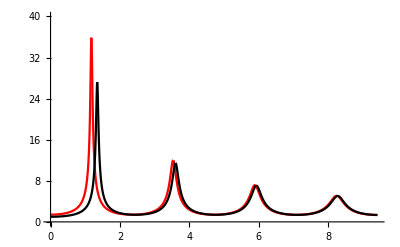

```mathematica
Plot[{Abs[TFGO[ALPHA,NN,r,DE]],Abs[TFR[ALPHA,NN,r,DE]]},{r,0,3π},PlotRange->{{0,3π},{0,40}},PlotStyle->{Red,Black}]
```

## Comparison of Geometrical Optics Approximation to numerical solution in two cases: hyperbolic distribution and sinusoidal distribution

Hyperbolic distribution (snap transition)

The next corresponds to eq.(3.37):

```mathematica
fhyp[η_,Δ_,p_,x0_]:=1-Δ/2*(1+Tanh[p(η-x0)])
```

The geometrical optics eq.(3.22):

```mathematica
TFGOhyp[r_,δ_,Δ_,p_,x0_]:=(1/Sqrt[fhyp[1,Δ,p,x0]])/Cos[NIntegrate[1/fhyp[x,Δ,p,x0],{x,0,1}]*r/Sqrt[(1+ⅈ*δ)]]
```

Sinusoidal distribution (profile reversal)

The next corresponds to eq.(3.38):

```mathematica
fsine[η_,Δ_,K_]:=1+Δ*Sin[K/2 π*η]
```

Likewise, for this distribution eq.(3.22) can be evaluated from

```mathematica
TFGOsine[r_,δ_,Δ_,K_]:=(1/Sqrt[fsine[1,Δ,K]])/Cos[NIntegrate[1/fsine[x,Δ,K],{x,0,1}]*r/Sqrt[(1+ⅈ*δ)]]
```

Numerical solution

## Parameters for the numerical simulation

First, set up the limit for the plots:

```mathematica
rmax=4*π;
```

Next, generate a list of points where the solution will be obtained (“rlist”), at a distance 0.01 between points. “L” represents the number of elements in that list.

```mathematica
rlist=Range[0,rmax,0.01];L=Length[rlist];
```

Generate the solution at each point (each element in “rlist”) solving an ODE where the actual evolution (either fsine and fhyp) is evaluated across the vertical discretization.

For the purpose of this document, fsine is used with the following parameters:

```mathematica
Δ2=0.9; K=5;
```

The damping factor (which is also in the plots in the text)

```mathematica
DE=0.01;
```

## Solving the ODE and saving the results

The next line contains a loop that solves the eq.(3.14), subjected to boundary conditions (3.15), for each value of dimensionless frequency in “rlist”.

```mathematica
For[i=1,i<L-1,i++,{solQ=NDSolve[{D[fsine[η,Δ2,K]^2* U'[η],η]+rlist[[i]]^2/(1+ⅈ*DE)*U[η]==1,U[0]==0,U'[1]==0},U,{η,0,1}],Result[i]=Evaluate[U[1]/.solQ]}]
```

The following array (table) allows for displaying the numerical results, while figA is the plot object that will be superimposed to the asymptotic solution so that the plots in either Figure 3.9 or Figure 3.10.

```mathematica
res1=Table[{rlist[[j]],Abs[1-rlist[[j]]^2/(1+ⅈ*DE)*Result[j][[1]]]},{j,L-1}];figA=ListPlot[res1,PlotRange->{{0,rmax},{0,45}},PlotStyle->{Black}];
```

Compare Transfer Functions

Evaluate the asymptotics, either fsine and fhyp, generate a plot image, figB, and superimpose it to figA to generate all the images of transfer functions Figure 3.9 and Figure 3.10.

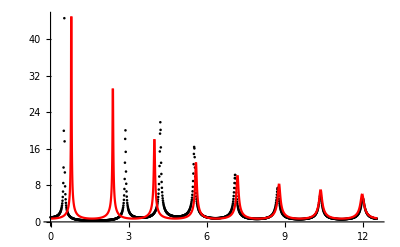

```mathematica
figB=Plot[{Abs[TFGOsine[r,DE,Δ2,K]]},{r,0,rmax},PlotStyle->{Red},PlotRange->{{0,rmax},{0,45}}]; Show[figA,figB]
```

(The one depicted by defect by the notebook corresponds to the middle tile in Figure3.10).